```mathematica
ClearAll["Global`*"]
```

```mathematica
(* For the prereheting scenario with inflaton potential , 
(1) we solve numerically the background (inflaton , Hubble ),the daughter mode function  and number density  for different  modes. In the spectator dynamics , we neglet the contribution from universe's expansion.
(2) we plot the Power spectrum of the daughter field and the number density of the daughter specie.
(3) Finally, we compute the GW generation due to daughter energy stress tensor. *)
```

# Preheating scenario

```mathematica
Mpl=10^6;                   (* Planck mass [GeV] *)(* we fix it as 10^6 so m_phi = 10^-6 M_p = 1 *)
mϕ=6*10^-6;                    (* inflation mass [GeV] *) (* bounded by CMB *)
λ = 0.0;                                    (* self-coupling constant [adim]*)
g=10^-4;                                (* coupling constant ϕ-χ [adim]*)
zMax=50;               (* ztime [adim] , time [GeV]^-1 *)
Φ0=0.1 Mpl;                           (* initial amplitude ϕ [GeV] *)
```

```mathematica
zMax//N
Φ0
```

60000.

100000.

## Solving Background dynamic

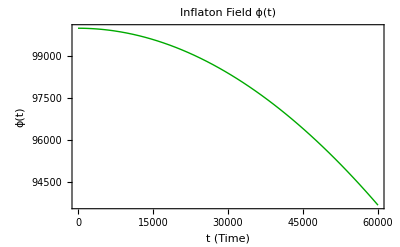

```mathematica
(* Background equations: EOM Inflaton field, Friedman equation *)
H[ϕ_,dϕ_]:=√(1/(3 Mpl^2)(1/2 dϕ^2 + 1/2 mϕ^2 ϕ^2+ λ/4 ϕ^4));
eqa = a'[t]==a[t]*H[ϕ[t],ϕ'[t]];
eqϕ=ϕ''[t]+3H[ϕ[t],ϕ'[t]]ϕ'[t]+mϕ^2 ϕ[t]+λ ϕ[t]^3==0;

(*Initial conditions*)
backgroundconditions = {a[0]==1,ϕ[0]==Φ0,ϕ'[0]==0};

(* Solve Background dynamic *)
solbackground=NDSolve[{eqϕ,eqa,backgroundconditions[[1]],backgroundconditions[[2]],backgroundconditions[[3]]},{ϕ,a},{t,0,zMax},Method->"StiffnessSwitching",MaxSteps->Infinity];

(* Solution's background *)
ϕsol[t_]:=Evaluate[ϕ[t]/. solbackground[[1]]];
asol[t_]:=Evaluate[a[t]/. solbackground[[1]]];
Hsol[t_]:=H[ϕsol[t],ϕsol'[t]];

ϕPlot = Plot[ϕsol[t],{t,0,zMax},PlotRange->All,PlotStyle->{Thick,Darker[Green]},Frame->True,FrameLabel->{"t (Time)","ϕ(t)"},PlotLabel->"Inflaton Field ϕ(t)"]
```

## Daughter dynamic

```mathematica
(* Frequency *)
ω2[t_,k_]:=k^2+g^2 ϕsol[t]^2;
ω[t_,k_]:=√ω2[t,k];

(* EOM daughter χ *)
eqχ=χ''[t]+ω2[t,k]*χ[t]==0;

(*Initial conditions*)
χconditions={χ[0]==1/(√(2ω[0,k])),χ'[0]==-I*√(ω[0,k]/2)}; (* Initial conditions  to be valued at  *)

(*Solve χ dynamic *)
solχ=ParametricNDSolveValue[{eqχ,χconditions[[1]],χconditions[[2]]},χ,{t,0,zMax},{k},MaxSteps->Infinity,Method->"StiffnessSwitching"];

(* Daughter solution *)
χsol[k_,t_]:=solχ[k][t];

(* Number density particles *)
numberχ[t_,k_] := Module[{χsolK},
χsolK = solχ[k];
Abs[χsolK'[t]]^2/ω[t,k]+ω[t,k]/2 Abs[χsolK[t]]^2-1/2
];
```

## Evaluate for specific momenta

$Aborted

$Aborted

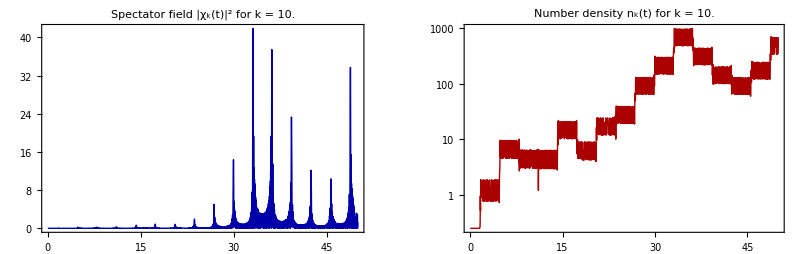

```mathematica
kexample = 10.0;
χPlot = Plot[Abs[χsol[kexample,t]]^2,{t,0,zMax},PlotRange->All,PlotStyle->{Thick,Darker[Blue]},Frame->True,PlotLabel->Style[StringForm["Spectator field |χ_k(t)|^2 for k = ``",kexample]]];
nχPlot = LogPlot[numberχ[t,kexample],{t,0,zMax},PlotRange->All,PlotStyle->{Thick,Darker[Red]},Frame->True,PlotLabel->Style[StringForm["Number density n_k(t) for k = ``",kexample]]];
GraphicsGrid[Partition[{χPlot,nχPlot},2,2,{1,2},""]]
```

## Resonance parameter

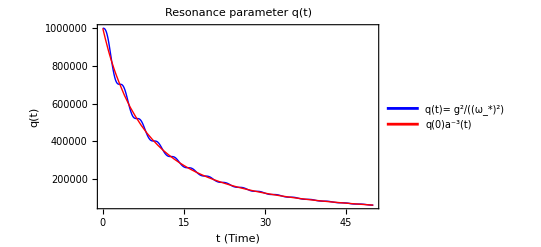

(Broad resonance regime) Maximum resonance parameter: 1.×10^6

Parametric resonance up to k_* = q^(1/4) = 31.6228

```mathematica
ωstar[Φ_,t_]:=√(mϕ^2+ 3λ Φ[t]^2);
Φ[t_]:=√(ϕsol[t]^2 + (ϕsol'[t])^2/ωstar[ϕsol,t]^2);
q[t_]:=(g^2 Φ[t]^2)/ωstar[Φ,t]^2; (* definition *)
Plot[{q[t],q[0]*asol[t]^-3},{t,0,zMax},PlotRange->All,PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,FrameLabel->{"t (Time)","q(t)"},PlotLegends->{"q(t)= g^2/(ω_*)^2","q(0)a^-3(t)"},PlotLabel->"Resonance parameter q(t)"]
If[q[0]>1,Print["\n (Broad resonance regime) Maximum resonance parameter: ",q[0]],Print["\n (Narrow resonance regime) Maximum resonance parameter: ",q[0]]];
Print["\n Parametric resonance up to k_* = q^(1/4) = ",q[0]^(1/4)]
```

## Power spectrum of the Daughter field

```mathematica
PSχ[k_,τ_]:=k^3/(2 π^2)  Abs[χsol[k,τ]]^2 ;

χSpectrum[kList_List,τ_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,PSχ[k,τ]},{k,kList}],Row[{"Computation χ for k = ",currentK}]]
];

nχSpectrum[kList_List,τ_]:=Module[{currentK},
Monitor[Table[currentK=k;
{k,numberχ[τ,k]},{k,kList}],Row[{"Computation nχ for k = ",currentK}]]
];
```

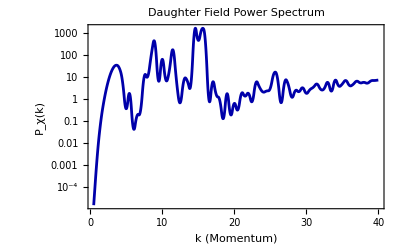

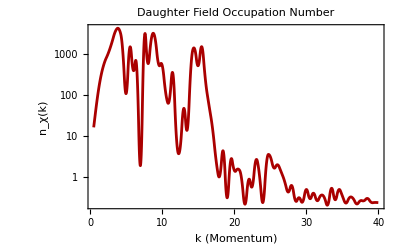

```mathematica
(* Range values *)
kValsχ=Range[0.5,40.0,0.5];

spectrumχ=χSpectrum[kValsχ,zMax];
spectrumnχ=nχSpectrum[kValsχ,zMax];

(* Plot *)
plotSpectrumχ=ListLogPlot[spectrumχ,Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"k (Momentum)","P_χ(k)"},PlotStyle->{Thickness[0.005],Darker[Blue]},GridLines->Automatic,PlotLabel->"Daughter Field Power Spectrum"]

plotSpectrumnχ=ListLogPlot[spectrumnχ,Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,FrameLabel->{"k (Momentum)","n_χ(k)"},PlotStyle->{Thickness[0.005],Darker[Red]},GridLines->Automatic,PlotLabel->"Daughter Field Occupation Number"]
```

# GW

## Compute the Power spectrum of GWs

```mathematica
(*  ,  *)
TimeIntegral[k_,p_,x_,τ_]:=Module[{kp,Ic,Is},
kp=Sqrt[k^2+p^2-2*k*p*x];

Quiet[
Ic=NIntegrate[Cos[k*t]*χsol[p,t]*χsol[kp,t],{t,0,τ},Method->"LocalAdaptive",MaxRecursion->15,AccuracyGoal->5,PrecisionGoal->5];
Is=NIntegrate[Sin[k*t]*χsol[p,t]*χsol[kp,t],{t,0,τ},Method->"LocalAdaptive",MaxRecursion->15,AccuracyGoal->5,PrecisionGoal->5];
];

(*  *)
(1-x^2)^2*(Abs[Ic]^2+Abs[Is]^2)*p^6
];

(*  *)
GWGrid[k_,τ_,pMax_:10.0,dp_:0.5,dx_:0.1]:=Module[{grid},
grid=Flatten[ParallelTable[{{p,x},TimeIntegral[k,p,x,τ]},{p,0.01,pMax,dp},{x,-1.0,1.0,dx}],1];
grid
];

funzρGWO[k_,τ_,pMax_:10.0,dp_:0.5,dx_:0.1]:=Module[{gridData,interpFunc,res},
gridData=GWGrid[k,τ,pMax,dp,dx];
interpFunc=Interpolation[gridData,InterpolationOrder->2];

(* integrate *)
res=NIntegrate[interpFunc[p,x],{p,0.01,pMax},{x,-1,1},Method->"GlobalAdaptive",AccuracyGoal->4,PrecisionGoal->4];
k^3/(2 π^3) *res
];

GWSpectrum[kList_List,τ_,pMax_:10.0,dp_:0.5,dx_:0.1]:=Module[{currentK},

Monitor[Table[currentK=k;{k,funzρGWO[k,τ,pMax,dp,dx]},{k,kList}],Row[{"Calculating spectrum... currently evaluating k = ",currentK}]]
];
```

## Power spectrum

```mathematica
DiscreteTimeIntegral[k_,p_,x_,τ_,tSteps_:150]:=Module[{tList,dt,χ1,χ2,kp,cosVec,sinVec,IntegrandCos,IntegrandSin,Ic,Is},
kp=Sqrt[k^2+p^2-2*k*p*x];
dt=τ/tSteps;
tList=Range[0.,τ,dt];

χ1=Table[χsol[p,t],{t,tList}];
χ2=Table[χsol[kp,t],{t,tList}];

cosVec=Cos[k*tList];
sinVec=Sin[k*tList];

IntegrandCos=cosVec*χ1*χ2;
IntegrandSin=sinVec*χ1*χ2;

Ic=(dt/2)*(IntegrandCos[[1]]+2*Sum[IntegrandCos[[i]],{i,2,tSteps}]+IntegrandCos[[-1]]);
Is=(dt/2)*(IntegrandSin[[1]]+2*Sum[IntegrandSin[[i]],{i,2,tSteps}]+IntegrandSin[[-1]]);

(1-x^2)^2*(Abs[Ic]^2+Abs[Is]^2)*p^6
];


FastGWSpectrumPoint[k_,τ_,pMax_:10.0,dp_:0.5,dx_:0.1,tSteps_:150]:=Module[{pList,xList,totalSum,pVal,xVal,term},
pList=Range[0.05,pMax,dp];
xList=Range[-0.95,0.95,dx];

totalSum=ParallelSum[term=DiscreteTimeIntegral[k,pVal,xVal,τ,tSteps];
term*dp*dx,{pVal,pList},{xVal,xList}];
(k^3/(2*Pi^3))*totalSum];

(*3. Spectrum Wrapper*)
FastGWSpectrum[kList_List,τ_,pMax_:10.0,dp_:0.5,dx_:0.1,tSteps_:150]:=Module[{currentK,result},
Monitor[result=Table[currentK=k;
{k,FastGWSpectrumPoint[k,τ,pMax,dp,dx,tSteps]},{k,kList}];
result,Row[{"Evaluating GW point for k = ",currentK}]]];
```

```mathematica
kValsGW=Range[0.2,8,0.2];
spectrumGW=FastGWSpectrum[kValsGW,tMax];
```

```mathematica
DiscreteTimeIntegral[k_,p_,x_,τ_,dt_:0.01]:=Module[{tList,χ1,χ2,kp,cosVec,sinVec,IntegrandCos,IntegrandSin,Ic,Is},
kp=Sqrt[k^2+p^2-2*k*p*x];
tList=Range[0.,τ,dt];

Quiet[
χ1=solχ[p][tList];
χ2=solχ[kp][tList];
];
cosVec=Cos[k*tList];
sinVec=Sin[k*tList];

IntegrandCos=cosVec*χ1*χ2;
IntegrandSin=sinVec*χ1*χ2;

Ic=(dt/2)*(Total[IntegrandCos]*2-IntegrandCos[[1]]-IntegrandCos[[-1]]);
Is=(dt/2)*(Total[IntegrandSin]*2-IntegrandSin[[1]]-IntegrandSin[[-1]]);

(1-x^2)^2*(Abs[Ic]^2+Abs[Is]^2)*p^6
];


FastGWSpectrumPoint[k_,τ_,pMax_:10.0,dp_:0.1,dx_:0.05]:=Module[{pList,xList,totalSum,pVal,xVal,term},
pList=Range[0.05,pMax,dp];
xList=Range[-0.95,0.95,dx];

totalSum=ParallelSum[term=DiscreteTimeIntegral[k,pVal,xVal,τ];
term*dp*dx,{pVal,pList},{xVal,xList}];
(k^3/(2*Pi^3))*totalSum
];


FastGWSpectrum[kList_List,τ_,pMax_:10.0,dp_:0.1,dx_:0.05]:=Module[{currentK,result},
Monitor[result=Table[currentK=k;
{k,FastGWSpectrumPoint[k,τ,pMax,dp,dx]},{k,kList}];
result,Row[{"Evaluating CORRECTED GW point for k = ",currentK}]]];
```

```mathematica
kValsGW=Range[0.1,8,0.5];
spectrumGW=FastGWSpectrum[kValsGW,tMax];
plotData=Transpose[{kValsGW,spectrumGW[[All,2]]}];

scientificPlot=ListLogPlot[plotData,Joined->True,InterpolationOrder->2,PlotRange->All,Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.004]],BaseStyle->{FontFamily->"Times",FontSize->14},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->500]
```

$Aborted

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6},Symbol[]} cannot be transposed.

ListLogPlot::lpn: { is not a list of numbers or pairs of numbers.

ListLogPlot[Transpose[{{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6},Symbol[]}],Joined→True,InterpolationOrder→2,PlotRange→All,Frame→True,Axes→False,PlotStyle→Directive[GrayLevel[0],Thickness[0.004]],BaseStyle→{FontFamily→Times,FontSize→14},GridLines→Automatic,GridLinesStyle→Directive[GrayLevel[0.8],Dashing[{Small,Small}]],ImageSize→500]

## Save data

```mathematica
(* Power spectrum χ *)
fileNameχCSV="DaughterSpectrumPreheating.csv";
fileNamenχCSV="DaughterNumberParticleSpectrumPreheating.csv";
fileNameGWCSV="GWSpectrumPreheating.csv";

Print["Saving data to: ",NotebookDirectory[],"\\",fileNameχCSV];
Export[fileNameχCSV,spectrumχ];
Print["Saving data to: ",NotebookDirectory[],"\\",fileNamenχCSV];
Export[fileNamenχCSV,spectrumnχ];
Print["Saving data to: ",NotebookDirectory[],"\\",fileNameGWCSV];
Export[fileNameGWCSV,spectrumGW];
```

Saving data to: C:\Users\sbart\Desktop\TESI MAGISTRALE\Codici\Preheating\\DaughterSpectrumPreheating.csv

Saving data to: C:\Users\sbart\Desktop\TESI MAGISTRALE\Codici\Preheating\\DaughterNumberParticleSpectrumPreheating.csv

Saving data to: C:\Users\sbart\Desktop\TESI MAGISTRALE\Codici\Preheating\\GWSpectrumPreheating.csv

```mathematica
(* Import the saved data
savedSpectrumχ = Import["DaughterSpectrumPreheating.csv"];
savedSpectrumnχ = Import["DaughterNumberParticleSpectrumPreheating.csv"];
savedSpectrumGW = Import["GWSpectrumPreheating.csv"]*)
```